```mathematica
i[x_]:=If[-1≤x≤1,1/2,0]
```

```mathematica
Clear[ConPow]
ConPow[f_,n_,x_]:=Module[{y},If[n==0,f[x],Convolve[ConPow[f,n-1,y],f[y],y,x]]]
```

```mathematica
Integrate[Convolve[i[x],i[x],x,y],{y,-1,1}]
```

3/4

```mathematica
Integrate[ConPow[i,#,x],{x,-1,1}]&/@Range[0,5]
```

{1,3/4,2/3,115/192,11/20,5887/11520}

```mathematica
2ConPow[i,#,0]&/@Range[0,7]
```

{1,1,3/4,2/3,115/192,11/20,5887/11520,151/315}

```mathematica
N@%89
```

{1.,1.,0.75,0.666667,0.598958,0.55,0.511024,0.479365}

```mathematica
Sqrt[6/Pi]//N
```

1.38198

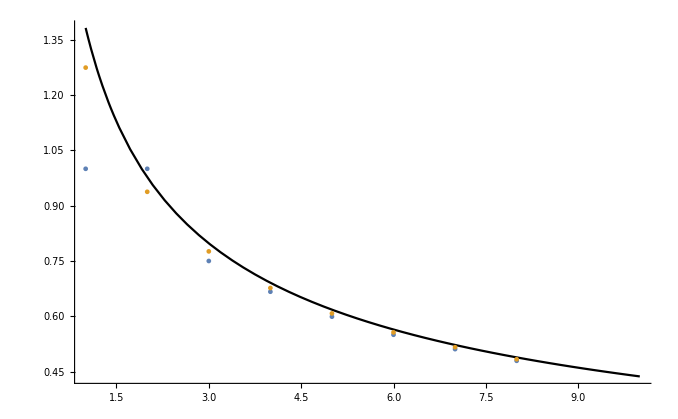

```mathematica
Show[Plot[√(6/(π x)),{x,1,10},PlotStyle->Black],ListPlot[{%89,%128},PlotStyle->PointSize[.005]]]
```

```mathematica
Sqrt[3]/2*(2/E)^(n+1)*(n+1)^n/(2^n*n!)/.n->Range[0,7]
```

{(√3)/ⅇ,(2 √3)/ⅇ^2,(9 √3)/(2 ⅇ^3),32/(√3 ⅇ^4),625/(8 √3 ⅇ^5),(324 √3)/(5 ⅇ^6),117649/(240 √3 ⅇ^7),131072/(105 √3 ⅇ^8)}

```mathematica
2*%//N
```

{1.27437,0.93763,0.776104,0.67677,0.607837,0.556415,0.516161,0.483542}

```mathematica
1/(1-(%89[[3;;]]/%89[[2;;-2]])^2)//N
```

{2.28571,4.76471,5.18645,6.37767,7.31486,8.32869}

```mathematica
%-Range[3,8]
```

{-0.714286,0.764706,0.186451,0.377674,0.314863,0.328693}

```mathematica
Sqrt[7./8]
```

0.935414

```mathematica
%91//N
```

0.938048

```mathematica
%54*(Range[1,6]!*2^Range[0,5])
```

{1,3,16,115,1056,11774}

```mathematica
ConPow[i,2][x]
```

1/2

```mathematica
ConPow[i,4,x]
```

Piecewise[{{1/48, x==3}, {11/48, x==-1||x==1}, {1/192 (55-10 x-30 x^2-10 x^3-x^4), -3<x<-1}, {1/192 (55+10 x-30 x^2+10 x^3-x^4), 1<x<3}, {1/768 (625-500 x+150 x^2-20 x^3+x^4), 3<x<5}, {1/768 (625+500 x+150 x^2+20 x^3+x^4), -5<x≤-3}, {1/384 (115-30 x^2+3 x^4), -1<x<1}, {0, True}}]

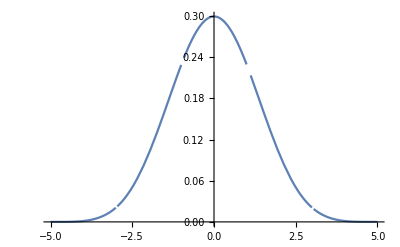

```mathematica
Plot[Piecewise[{{1/48, x==3}, {11/48, x==-1||x==1}, {1/192 (55-10 x-30 x^2-10 x^3-x^4), -3<x<-1}, {1/192 (55+10 x-30 x^2+10 x^3-x^4), 1<x<3}, {1/768 (625-500 x+150 x^2-20 x^3+x^4), 3<x<5}, {1/768 (625+500 x+150 x^2+20 x^3+x^4), -5<x≤-3}, {1/384 (115-30 x^2+3 x^4), -1<x<1}, {0, True}}],{x,-5,5}]
```

```mathematica
ConPow[i,2,y]
```

Piecewise[{{1/8 (3-y^2), -1<y≤1}, {1/16 (-3+y)^2, 1<y<3}, {1/16 (3+y)^2, -3<y≤-1}, {0, True}}]

```mathematica
Convolve[ConPow[i,1][y],i[y],y,x]
```

1/2

```mathematica
Convolve[f[x],g[x],x,y]
```

Convolve[f[x],g[x],x,y]

```mathematica
est[n_]:=√(3/(2 π n))
```

```mathematica
2*(est/@Range[8]//N)
```

{1.38198,0.977205,0.797885,0.690988,0.618039,0.56419,0.522338,0.488603}